```mathematica
Clear[x,n,r,Ni,t,Maximum,Pr,c1,a,Bound,Snorm];
n[k_Integer]:=n[k]=Floor[(x[k]+1)/3];r[k_Integer]:=r[k]=Mod[x[k],3](5-3 Mod[x[k],3])/2;x[0]=44;x[k_Integer]:=x[k]=2(1+r[k-1]^2)n[k-1]+r[k-1]
```

```mathematica
c1=Table[x[i],{i,0,100}]
```

{44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70,93,62,83,111,74,99,66,44,59,79,105,70}

```mathematica
a=Table[Log[(x[i]-((2*1000)/3))/Sqrt[1000 2/3 1/3]],{i,0,1000}];(*Iterated log approximation for the usages of A*)
```

```mathematica
b=Table[(x[i]-((2*1000)/3))/Sqrt[1000 2/3 1/3],{i,0,1000}];
```

```mathematica
a[1];
```

```mathematica
N[Max[b]]
```

-37.2753

```mathematica
N[62014718689772031011303309/(20 √(10 Log[Log[1000]]))]
```

7.05324×10^23

```mathematica
Max[b]/Sqrt[2Log[Log[1000]]]
```

-1667/(20 √(10 Log[Log[1000]]))

```mathematica
N[(3 (-2000/3+62014718689772031011303309/(20 √5)))/(20 √(10 Log[Log[1000]]))]
```

4.73146×10^22

```mathematica
Ni=10000;
```

```mathematica
t=1;
```

```mathematica
Maximum4[t_]:=Ni*1/3+t Sqrt[2 Ni 2/3 1/3 Log[Log[Ni]]](*iterated log for diffent values of lambda*)
```

```mathematica
N[Maximum4]
```

Maximum4

```mathematica
d=Table[Mod[x[i],3],{i,0,10000}];
```

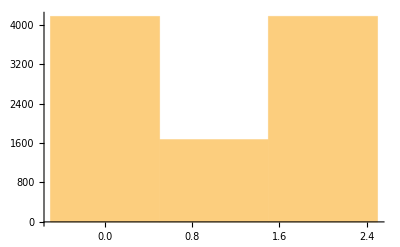

```mathematica
Histogram[d]
```

```mathematica
Table[N[Maximum4[i]],{i,1,10}]
```

{3432.67,3532.01,3631.35,3730.69,3830.03,3929.36,4028.7,4128.04,4227.38,4326.72}

```mathematica
Max[a]
```

Max::nord: Invalid comparison with ⅈ π+Log[1667/(20 √5)] attempted.

Max::nord: Invalid comparison with ⅈ π+Log[337/(4 √5)] attempted.

Max::nord: Invalid comparison with ⅈ π+Log[1703/(20 √5)] attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Max[ⅈ π+Log[1667/(20 √5)],ⅈ π+Log[337/(4 √5)],ⅈ π+Log[1703/(20 √5)],ⅈ π+Log[1721/(20 √5)],ⅈ π+Log[1751/(20 √5)],ⅈ π+Log[1763/(20 √5)],ⅈ π+Log[889/(10 √5)],ⅈ π+Log[179/(2 √5)],ⅈ π+Log[901/(10 √5)],ⅈ π+Log[907/(10 √5)],ⅈ π+Log[1823/(20 √5)],ⅈ π+Log[467/(5 √5)]]

```mathematica
c=Table[x[i],{i,0,1000}];
```

```mathematica
Maximum2[t_]:=Ni*1/3+t Sqrt[2 Ni *2/3 1/3 Log[Log[Ni]]]
```

```mathematica
Table[N[Maximum2[i]],{i,0,10}]
```

{3333.33,3432.67,3532.01,3631.35,3730.69,3830.03,3929.36,4028.7,4128.04,4227.38,4326.72}

```mathematica
Usagereal=N[416/Ni]
```

0.0416

```mathematica
Prusage=N[Maximum2[3]]/Ni
```

0.363135

```mathematica
Ex=1/3 2/3 + 2/3 4/3;
```

```mathematica
nq=Table[N[Maximum2[i]],{i,1,10}]
```

{3432.67,3532.01,3631.35,3730.69,3830.03,3929.36,4028.7,4128.04,4227.38,4326.72}

```mathematica
np=Table[N[Maximum4[i]],{i,1,10}]
```

{3432.67,3532.01,3631.35,3730.69,3830.03,3929.36,4028.7,4128.04,4227.38,4326.72}

```mathematica
nq1=362.6412369614301;np1=Ni-nq1;
```

```mathematica
Pr=Binomial[1000,nq1]*(1/3)^nq1 *(2/3)^np1
```

General::munfl: (2/3)^9637.36 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
nq2=Ni-np2;np2=695.9745702947633;
```

```mathematica
Pr2=Binomial[1000,nq2](1/3)^nq2 *(2/3)^np2
```

General::munfl: (2.73029×10^-6)/(6.58062786728221×10^1376) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1/3)^9304.03 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
(*Analysis*)
```

```mathematica
route1=(4/3)^np2 (2/3)^nq2
```

General::munfl: (2/3)^9304.03 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
route2=(4/3)^np1 (2/3)^nq1
```

1.66523715714056×10^1140

```mathematica
Simplify[Max[c]]
```

111

```mathematica
route1-20671572896590677003768393
```

-2.06716×10^25

```mathematica
(*Ballot theorem*)
```

```mathematica
pb=1000-qb;qb=335;
```

```mathematica
B=Binomial[Ni-1,pb-1]-Binomial[Ni-1,pb]
```

-8888200459486429314691720063678604937373722079399029465419191737195970000319937902078185553553014612234833498374185627795700307183425843635563232721989716973100681427991310626803753419142482496509804233890552558699185414740420548646344829662119085471790151065998913907464841951788686825225710026849377940399632059386372627438164890656413167492983329874849147585051223386289807746717155196966278601129114581862851864680235452546365519950853312641316793577699133133114611983383646325906296350499266203327804178575377816577636299782017332637060222908731518053782450238419021199625492889412568740069609354814601989933877232745653578080659235300696923160630700741121499373266867832272374458889096071086906390646224136461949541729329517184462762499642807975764148349494679191814568735193375777960772991098271086546574778663525578971679271865522725479912800121917348802040462602091467381343952828814457300239207481531584673394150984283344495904109458774673751252560424117085943692855303852228348160951184605771090304792865930146178955466967779165221778430164422269280

```mathematica
N[B]
```

-8.88820045948643×10^1059

```mathematica
(*Coomparison*)
Show[ListPlot[a],Plot[Sqrt[2*Log[Log[n]]],{n,0,1000}]]
```

-Graphics-

```mathematica
Bound[a_]:=Sqrt[N[2*a*Log[Log[1000]]]]
```

```mathematica
Snorm[s_]:=N[(s-1000 1/3)/Sqrt[1000 1/3 2/3]]
```

```mathematica
Snorm[416]
```

5.54545

```mathematica
Snorm[335]
```

0.111803

```mathematica
Bound[8]
```

5.56078